```mathematica
<<Vilcretas`
```

VilCretas está disponible.

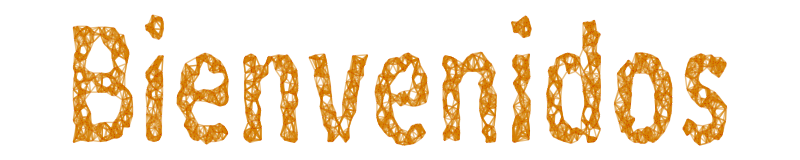

```mathematica
GrafoString["Bienvenidos"]
```

```mathematica
Sumatoria1[n_]:=If[n==6, 1/2, (n-5)/(n-4)+Sumatoria1[n-1]]
```

```mathematica
Sumatoria1[10]
```

71/20

```mathematica
1/(1+1)
```

1/2

```mathematica
Sumatoria2[n_]:=If[n==9,49/262144, ((n+5)/2^(n+1))^2+ Sumatoria2[n-1]]
```

```mathematica
Sumatoria2[10]
```

1009/4194304

```mathematica
Table[Sumatoria1[n]==Sum[i/(i+1),{i, 1, n-5}],{n, 6, 15}]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
(14/2^(14-4))^2
```

49/262144

```mathematica
Productoria1[n_]:=If[n==11,2,Productoria1[n-1]*((3*n)-31)]
```

```mathematica
Productoria1[15]
```

12320

3 i - 1
3 n - 1
3 (n - 10) - 1

```mathematica
ProductoriaAux[n_]:=If[n==3,-1,If[n==1||n==2, 1,ProductoriaAux[n-1]*(2*n - 7)]]
```

```mathematica
Sumatoria3[n_]:=If[n==0,1,Sumatoria3[n-1]+ProductoriaAux[n+1]*(n+1)]
```

```mathematica
Sumatoria3[3]
```

-4

Or[] o bien ||
And[] o bien &&

2 n - 5
2 (n - 1) - 5
2 n - 2 - 5 = 2 n - 7

```mathematica
<<TutoriasED`
```

Se ha cargado el paquete TutoriasED. USO PARA ESTUDIO

```mathematica
FibonacciPilaED[15, show->True]
```

Set::write: Tag List in {}[1] is Protected.

Set::write: Tag List in {}[0] is Protected.

Set::write: Tag List in {}[2] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

-Graphics-

610

```mathematica
fib[n_]:=If[n==1,1, If[n==0,0, fib[n-1]+fib[n-2]+fib[n-3]]]
```

```mathematica
fib[5]
```

Se debe tener tantos If como casos base

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

TerminatedEvaluation[RecursionLimit]+fib[5-2]+fib[5-3]

```mathematica
?GrafoDato
```

```mathematica
buscarDato[lista_, dato_]:=If[Last[lista]==dato, Print["Dato encontrado: ", lista], 
If[lista=={}, Print["Dato no encontrado"],Print[lista]];
 buscarDato[Delete[lista, Length[lista]], dato];
]
```

```mathematica
list = {1,2,3,4,5,6,7,"Ocho","a"};
```

```mathematica
buscarDato[list, 7]
```

{1,2,3,4,5,6,7,Ocho,a}

{1,2,3,4,5,6,7,Ocho}

Dato encontrado: {1,2,3,4,5,6,7}

```mathematica
Clear[list] (*Para limpiar x nombre de variable/función*)
```